```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\刘兴瑞\Documents\Visual Studio 2015\Projects\gears\gears

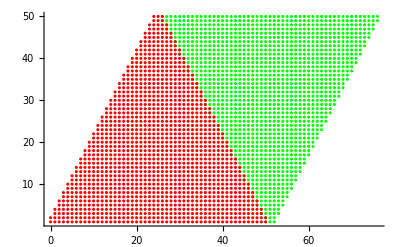

```mathematica
ileft1=ReadList[TemplateApply["i_left1_``.txt",{1}],Number];
ileft2=ReadList[TemplateApply["i_left2_``.txt",{1}],Number];
iright1=ReadList[TemplateApply["i_right1_``.txt",{1}],Number];
iright2=ReadList[TemplateApply["i_right2_``.txt",{1}],Number];
iplot={};
itooth1={};
itooth2={};
Do[Do[itooth1=Append[itooth1,{ileft1[[i]]+j-1,i}],
{j,1,iright1[[i]]-ileft1[[i]]+1}];Do[itooth2=Append[itooth2,{ileft2[[i]]+j-1,i}],
{j,1,iright2[[i]]-ileft2[[i]]+1}],
{i,1,Length[ileft1]}];
ip1=ListPlot[itooth1,PlotStyle->Red];
ip2=ListPlot[itooth2,PlotStyle->Green];
Show[ip2,ip1,PlotRange->All]
```

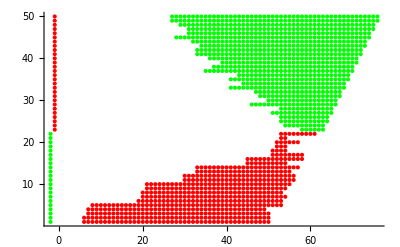

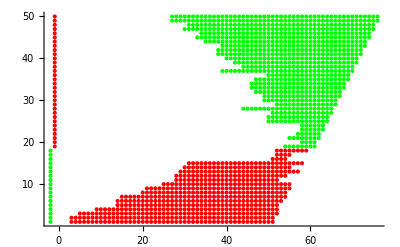

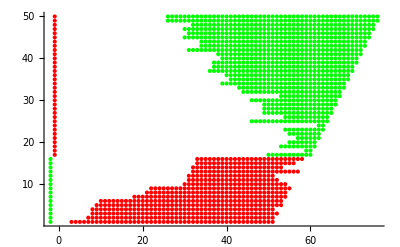

```mathematica
Do[left1=ReadList[TemplateApply["left1_``.txt",{k}],Number];
left2=ReadList[TemplateApply["left2_``.txt",{k}],Number];
right1=ReadList[TemplateApply["right1_``.txt",{k}],Number];
right2=ReadList[TemplateApply["right2_``.txt",{k}],Number];
tooth1={};
tooth2={};
Do[Do[tooth1=Append[tooth1,{left1[[i]]+j-1,i}],
{j,1,right1[[i]]-left1[[i]]+1}];Do[tooth2=Append[tooth2,{left2[[i]]+j-1,i}],
{j,1,right2[[i]]-left2[[i]]+1}],
{i,1,Length[left1]}];
p1=ListPlot[tooth1,PlotStyle->Red];
p2=ListPlot[tooth2,PlotStyle->Green];
Print[Show[p2,p1,PlotRange->All]],{k,1,3}]
```

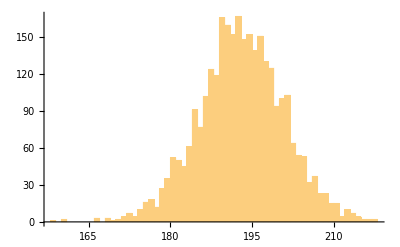

```mathematica
failTime=Flatten[Import["fail_time.csv"]];
Histogram[failTime,100]
```